```mathematica
Remove["Global`*"]
```

```mathematica
NormFactor = 1/NIntegrate[Sin[x]*Sin[x],{x,0,Pi}]
```

0.63662

```mathematica
xSqSinCoeffs = NormFactor*Table[NIntegrate[x^2*Sin[k*x],{x,0,Pi}],
{k,1,10}]

xSqCosCoeffs = NormFactor*Table[NIntegrate[x^2*Cos[k*x],{x,0,Pi}],{k,0,10}]
```

{3.73671,-3.14159,2.00008,-1.5708,1.23627,-1.0472,0.890174,-0.785398,0.694639,-0.628319}

{6.57974,-4.,1.,-0.444444,0.25,-0.16,0.111111,-0.0816327,0.0625,-0.0493827,0.04}

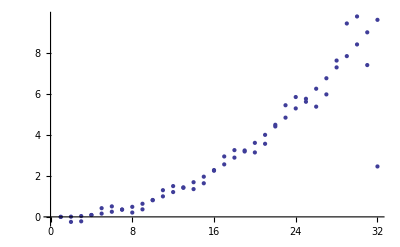

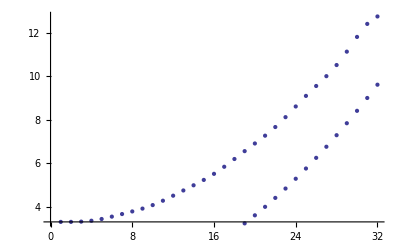

```mathematica
Show[ListPlot[Table[Sum[xSqSinCoeffs[[i]]*Sin[i*x],{i,1,10}],{x,0,Pi,0.1}]],ListPlot[Table[x^2,{x,0,Pi,0.1}]]]
Show[ListPlot[Table[Sum[xSqCosCoeffs[[i]]*Cos[(i-1)*x],{i,1,11}],{x,0,Pi,0.1}]],ListPlot[Table[x^2,{x,0,Pi,0.1}]]]
```

```mathematica
xCuSinCoeffs = NormFactor*Table[NIntegrate[x^3*Sin[k*x],{x,0,Pi}],
{k,1,10}]

xCuCosCoeffs = NormFactor*Table[NIntegrate[x^3*Cos[k*x],{x,0,Pi}],{k,0,10}]
```

{7.73921,-8.3696,6.13529,-4.7473,3.85184,-3.23431,2.7849,-2.44396,2.17678,-1.96192}

{15.5031,-11.2101,4.71239,-2.00008,1.1781,-0.741759,0.523599,-0.381503,0.294524,-0.231546,0.188496}

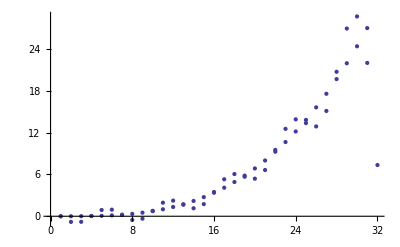

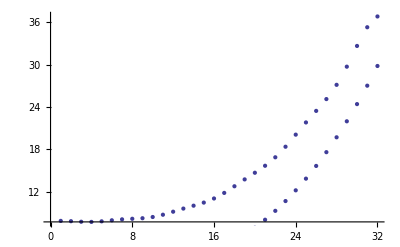

```mathematica
Show[ListPlot[Table[Sum[xCuSinCoeffs[[i]]*Sin[i*x],{i,1,10}],{x,0,Pi,0.1}]],ListPlot[Table[x^3,{x,0,Pi,0.1}]]]

Show[ListPlot[Table[Sum[xCuCosCoeffs[[i]]*Cos[(i-1)*x],{i,1,11}],{x,0,Pi,0.1}]],ListPlot[Table[x^3,{x,0,Pi,0.1}]]]
```

```mathematica
a=1; b=0;
nveExpSinCoeffs = 
NormFactor*Table[NIntegrate[Exp[-a*(x-b)^2]*Sin[k*x],{x,0,Pi}],{k,1,10}]

nveExpCosCoeffs = NormFactor*Table[NIntegrate[Exp[-a*(x-b)^2]*Cos[k*x],{x,0,Pi}],{k,0,10}]
```

{0.270205,0.342551,0.272634,0.191837,0.142022,0.113488,0.0952546,0.082343,0.0726335,0.0650182}

{0.564185,0.439396,0.207549,0.0594694,0.0103298,0.00109239,0.0000668262,5.09913×10^-6,-1.99182×10^-6,1.76635×10^-6,-1.52352×10^-6}

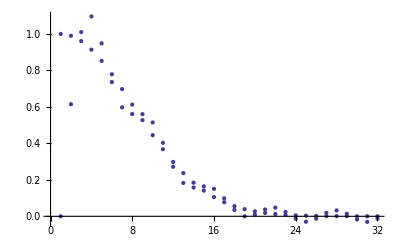

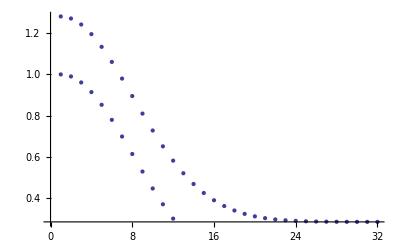

```mathematica
Show[ListPlot[Table[Sum[nveExpSinCoeffs[[i]]*Sin[i*x],{i,1,10}],{x,0,Pi,0.1}]],ListPlot[Table[Exp[-a*(x-b)^2],{x,0,Pi,0.1}]]]

Show[ListPlot[Table[Sum[nveExpCosCoeffs[[i]]*Cos[(i-1)*x],{i,1,11}],{x,0,Pi,0.1}]],ListPlot[Table[Exp[-a*(x-b)^2],{x,0,Pi,0.1}]]]
```

```mathematica
a=1; b=0;
pveExpSinCoeffs =NormFactor*Table[NIntegrate[Exp[a*(x-b)^2]*Sin[k*x],{x,0,Pi}],{k,1,10}]

pveExpCosCoeffs =NormFactor*Table[NIntegrate[Exp[a*(x-b)^2]*Cos[k*x],{x,0,Pi}],{k,0,10}]
```

{363.151,-648.555,839.383,-947.206,995.822,-1004.51,989.329,-959.845,923.377,-883.482}

{2079.92,-2006.71,1828.06,-1604.61,1379.52,-1174.72,997.889,-849.265,725.932,-624.046,539.847}

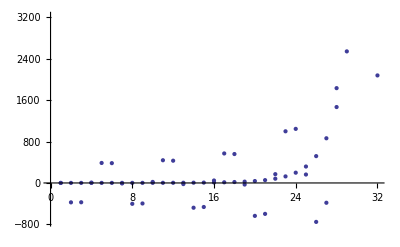

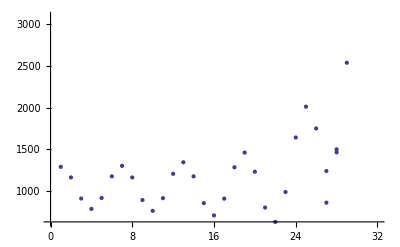

```mathematica
Show[ListPlot[Table[Sum[pveExpSinCoeffs[[i]]*Sin[i*x],{i,1,10}],{x,0,Pi,0.1}]],ListPlot[Table[Exp[a*(x-b)^2],{x,0,Pi,0.1}]]]

Show[ListPlot[Table[Sum[pveExpCosCoeffs[[i]]*Cos[(i-1)*x],{i,1,11}],{x,0,Pi,0.1}]],ListPlot[Table[Exp[a*(x-b)^2],{x,0,Pi,0.1}]]]
```

```mathematica
L=1
stepFnSinCoeffs =NormFactor*Table[NIntegrate[(1/L)*Sin[k*x],{x,0,1}],{k,1,10}]

stepFnCosCoeffs =NormFactor*Table[NIntegrate[(1/L)*Cos[k*x],{x,0,1}],{k,0,10}]
```

1

{0.292653,0.450774,0.42229,0.263186,0.091207,0.00422606,0.0223815,0.091156,0.135185,0.117079}

{0.63662,0.535697,0.289438,0.0299466,-0.120449,-0.122094,-0.0296469,0.0597501,0.0787306,0.0291514,-0.0346335}

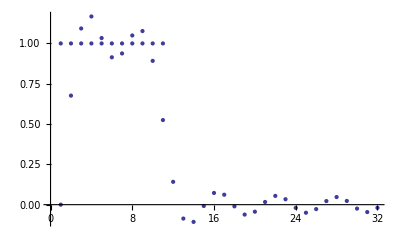

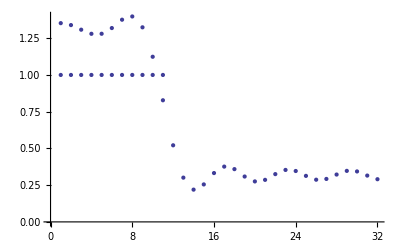

```mathematica
Show[ListPlot[Table[Sum[stepFnSinCoeffs[[i]]*Sin[i*x],{i,1,10}],{x,0,Pi,0.1}]],ListPlot[Table[(1/L),{x,0,1,0.1}]]]

Show[ListPlot[Table[Sum[stepFnCosCoeffs[[i]]*Cos[(i-1)*x],{i,1,11}],{x,0,Pi,0.1}]],ListPlot[Table[(1/L),{x,0,1,0.1}]]]
```